```mathematica
(*grades, anonymized, post-first stage processing*)
grades={{0,2,2,1,1,2,0},{1,1,2,3,3,2,1},{1,1,2,2,2,1,1},{1,2,1,2,1,2,1},{0,2,2,2,0,2,1},{0,1,1,2,3,0,1},{0,2,2,2,3,2,1},{0,2,2,1,1,1,0},{0,2,0,2,2,2,1},{1,2,1,1,3,2,1},{2,2,2,2,3,2,1},{0,2,1,1,2,1,1}};
```

```mathematica
(*messy way to take Transpose of grades & include test total scores*)
p1={};
p2={};
p3={};
p4={};
p5={};
p6={};
p7={};
total={};
For[i=1,i≤Length[grades],i++,
p1=Append[p1,grades[[i]][[1]]];
p2=Append[p2,grades[[i]][[2]]];
p3=Append[p3,grades[[i]][[3]]];
p4=Append[p4,grades[[i]][[4]]];
p5=Append[p5,grades[[i]][[5]]];
p6=Append[p6,grades[[i]][[6]]];
p7=Append[p7,grades[[i]][[7]]];
total=Append[total,Sum[grades[[i]][[k]],{k,1,7}]];
]
score={p1,p2,p3,p4,p5,p6,p7,total};
```

```mathematica
(*compute correlation matrix*)
corr=ConstantArray[0,{8,8}];
For[i=1,i≤8,i++,
For[j=1,j≤8,j++,
corr[[i]][[j]]=N[Correlation[score[[i]],score[[j]]]];
]
]
```

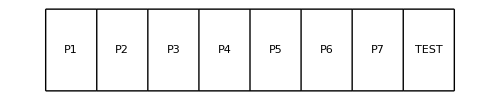
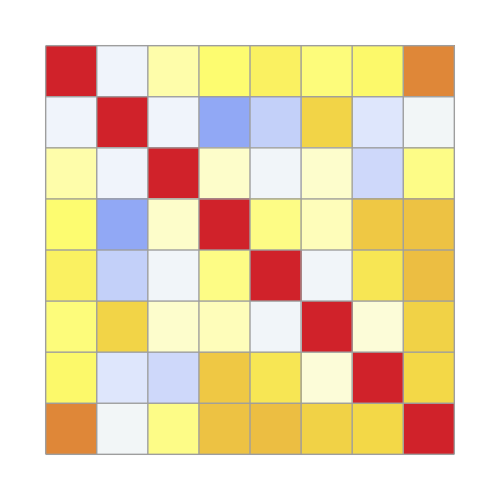
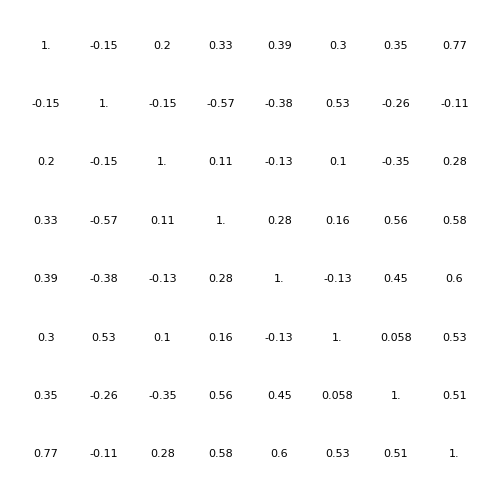
-Graphics-
-Graphics--Graphics--Graphics-

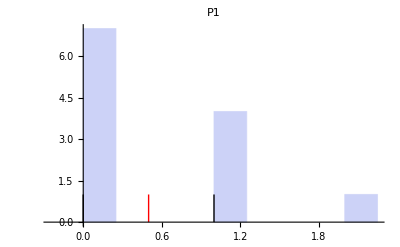
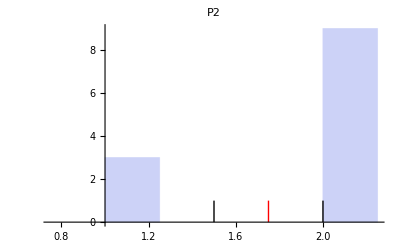
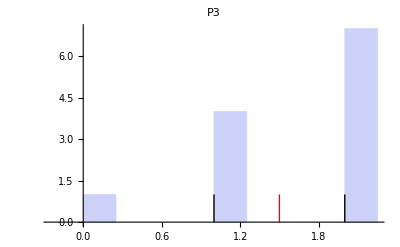
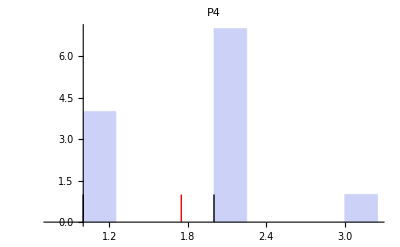
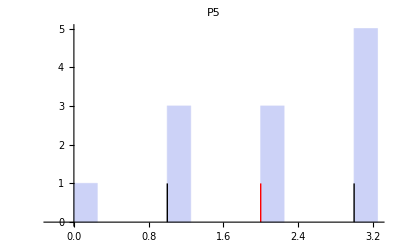
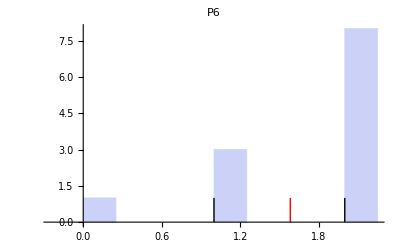
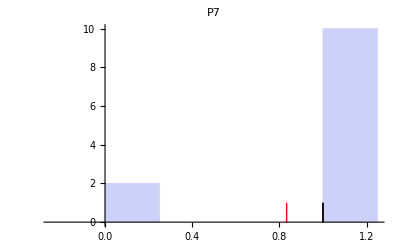
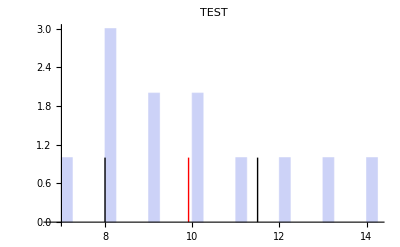

-Graphics-

```mathematica
(*labels for the correlation array*)
labels={P1,P2,P3,P4,P5,P6,P7,TEST};
(*Fancy picture*)
Column[{GraphicsRow[labels,ImageSize->500,Frame->All],Row[{GraphicsColumn[labels,ImageSize->63,Frame->All],Overlay[{ArrayPlot[corr,ColorFunction->(ColorData["TemperatureMap"][(1+#)/2]&),Frame->None,Mesh->True,PlotRangePadding->0,ImageSize->500,ColorFunctionScaling->False],GraphicsGrid[Map[NumberForm[#,2]&,corr,{2}],ImageSize->500]}]}]},Alignment->Right,Spacings->0]
(*histograms for each problem & test as a whole*)
histograms={};
For[i=1,i≤8,i++,
histograms=Append[histograms,Histogram[score[[i]],{.25},Epilog->{Directive[{Thick,Red}],Line[{{Mean[score[[i]]],0},{Mean[score[[i]]],1}}],{Directive[{Thick,Black}],Line[{{Quartiles[score[[i]]][[1]],0},{Quartiles[score[[i]]][[1]],1}}],Line[{{Quartiles[score[[i]]][[3]],0},{Quartiles[score[[i]]][[3]],1}}]}},PlotLabel->labels[[i]]]];
]
histograms
histograms[[8]]
```

```mathematica
(*exclude problem 1 from consideration*)
grades={{2,2,1,1,2,0},{1,2,3,3,2,1},{1,2,2,2,1,1},{2,1,2,1,2,1},{2,2,2,0,2,1},{1,1,2,3,0,1},{2,2,2,3,2,1},{2,2,1,1,1,0},{2,0,2,2,2,1},{2,1,1,3,2,1},{2,2,2,3,2,1},{2,1,1,2,1,1}};
```

```mathematica
p2={};
p3={};
p4={};
p5={};
p6={};
p7={};
total={};
For[i=1,i≤Length[grades],i++,
p2=Append[p2,grades[[i]][[1]]];
p3=Append[p3,grades[[i]][[2]]];
p4=Append[p4,grades[[i]][[3]]];
p5=Append[p5,grades[[i]][[4]]];
p6=Append[p6,grades[[i]][[5]]];
p7=Append[p7,grades[[i]][[6]]];
total=Append[total,Sum[grades[[i]][[k]],{k,1,6}]];
]
score={p2,p3,p4,p5,p6,p7,total};
```

```mathematica
corr=ConstantArray[0,{7,7}];
For[i=1,i≤7,i++,
For[j=1,j≤7,j++,
corr[[i]][[j]]=N[Correlation[score[[i]],score[[j]]]];
]
]
```

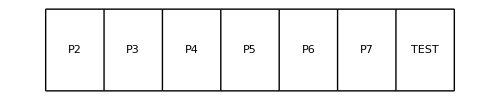
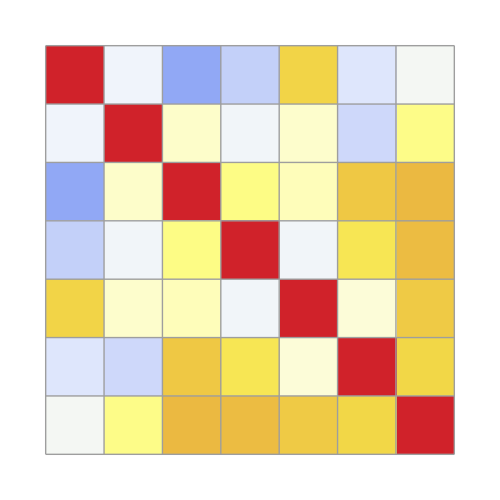
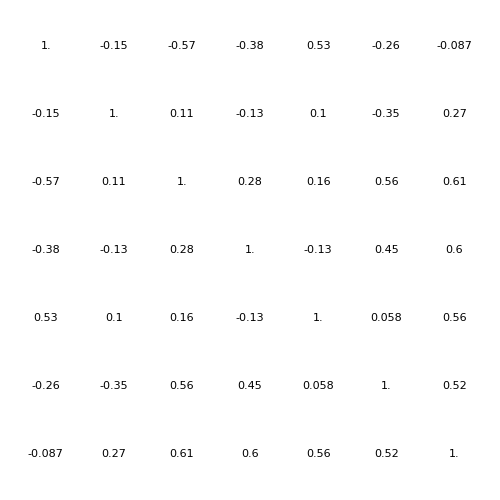
-Graphics-
-Graphics--Graphics--Graphics-

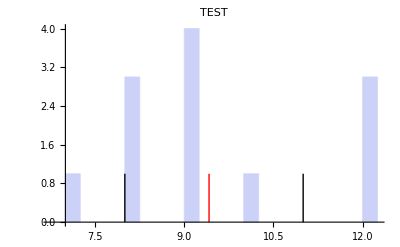
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

-Graphics-

```mathematica
labels={P2,P3,P4,P5,P6,P7,TEST};
Column[{GraphicsRow[labels,ImageSize->500,Frame->All],Row[{GraphicsColumn[labels,ImageSize->72,Frame->All],Overlay[{ArrayPlot[corr,ColorFunction->(ColorData["TemperatureMap"][(1+#)/2]&),Frame->None,Mesh->True,PlotRangePadding->0,ImageSize->500,ColorFunctionScaling->False],GraphicsGrid[Map[NumberForm[#,2]&,corr,{2}],ImageSize->500]}]}]},Alignment->Right,Spacings->0]
histograms={};
For[i=1,i≤7,i++,
histograms=Append[histograms,Histogram[score[[i]],{.25},Epilog->{Directive[{Thick,Red}],Line[{{Mean[score[[i]]],0},{Mean[score[[i]]],1}}],{Directive[{Thick,Black}],Line[{{Quartiles[score[[i]]][[1]],0},{Quartiles[score[[i]]][[1]],1}}],Line[{{Quartiles[score[[i]]][[3]],0},{Quartiles[score[[i]]][[3]],1}}]}},PlotLabel->labels[[i]]]];
]
histograms
histograms[[7]]
```